```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo1dot67.txt", "Table"];
```

dataLength will be 1000, this was just an experiment

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,78},{1,68},{2,74},{3,53},{4,52},{5,49},{6,51},{7,38},{8,40},{9,31},{10,39},{11,29},{12,17},{13,40},{14,25},{15,29},{16,17},{17,20},{18,20},{19,22},{20,9},{21,8},{22,15},{23,14},{24,9},{25,10},{26,10},{27,6},{28,13},{29,7},{30,9},{31,9},{32,7},{33,7},{34,5},{35,6},{36,3},{37,4},{38,5},{39,5},{40,5},{41,2},{42,3},{43,4},{44,5},{45,2},{46,2},{47,4},{48,0},{49,1},{50,0},{51,3},{52,1},{53,1},{54,0},{55,2},{56,2},{57,1},{58,2},{59,2},{60,0},{61,0},{62,0},{63,0},{64,1},{65,0},{66,0},{67,0},{68,0},{69,1},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,1},{81,1},{82,0},{83,0},{84,0},{85,1}}

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

12.456

```mathematica
probDensFunc[x_]:=N[probabilityData[[x+1,2]]/dataLength]
```

```mathematica
probDensFunc[0]
```

0.078

http://math.bme.hu/~nandori/Virtual_lab/stat/expect/Generating.pdf

```mathematica
probGenFunc[z_]:=Sum[probDensFunc[n]*(z^n),{n,0,Max[cleanData]}]
```

```mathematica
probGenFunc[0.01]
```

0.0786875

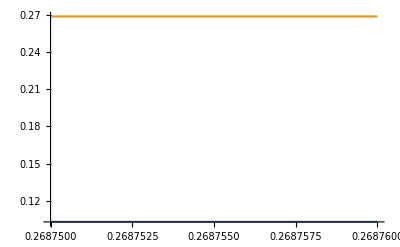

```mathematica
Plot[{probGenFunc[t],t},{t,0.26875,0.26876}]
```

```mathematica
probGenFunc[0.2687]
```

0.103007